## Example calculation for solving bound state of two fermions interacting via Yukawa potential

Let us perform an example calculation for Appendix A of the manuscript “Two Body Bound States through Yukawa Forces and Perspectives on Hydrogen.” Assume that we are picking up at equation (A1), and that our δ = 1, along with l = 0.

```mathematica
V[ρ_]:= (- 2Exp[-ρ])/ρ
```

We get the corresponding radial equation from (A2), working with the reduced radial function.

```mathematica
radialEq:=V[ρ]u[ρ]-u''[ρ];
```

We then perform a trig substitution to rescale to a finite domain, which Mathematica can handle better.

```mathematica
radialξ:=Simplify[radialEq/.u->(ψ[ArcTan[#]]&)/.ρ->(Tan[ξ]),Pi/2>ξ>0];
```

Add in the shift and calculate, then remove the shift.

```mathematica
shift=20;
solns = NDEigensystem[{radialξ+shift ψ[ξ],DirichletCondition[ψ[ξ]==0,True]},ψ,{ξ,0,Pi/2},5,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}},"Eigensystem"->{"Arnoldi",MaxIterations->50000}}];
solns[[1]]=solns[[1]]-shift;
```

```mathematica
solns[[1]]
```

{-0.0205716,0.0000736156,0.000649952,0.00242275,0.00675966}

Note that the ground state is bound, while the next excited state with zero orbital angular momentum is not. This is reflected in their corresponding radial probability distributions. We can plot the (unnormalized) ground state radial probability distribution after rescaling our domain and radial function. Note that our distance here is in terms of Bohr radii.

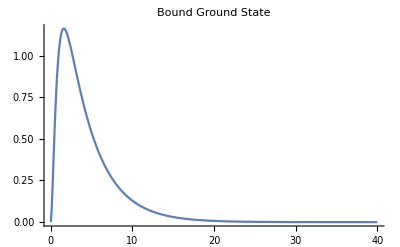

```mathematica
Plot[solns[[2,1]][ArcTan[x]]^2,{x,0,40}, PlotRange->All, PlotLabel->"Bound Ground State"]
```

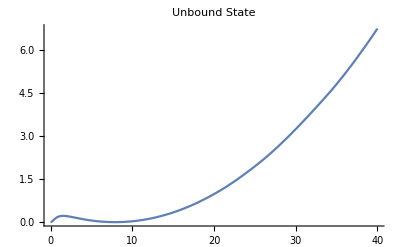

```mathematica
Plot[solns[[2,2]][ArcTan[x]]^2,{x,0,40}, PlotRange->All, PlotLabel->"Unbound State"]
```

## Tabulating solutions over parameters of a given potential

This section is designed to solve for the eigensystem of two particles interacting according to Schrodinger’s equation, over a given parameter range.

```mathematica
(* plug in desired potential here *)
```

```mathematica
V[r_]:= (- Exp[-r/δs])/r+γ Exp[-r/δv]/r;
```

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)]
vrange=logspace[-2,1,100]; (*δv from 0.1 to 10 *)
srange=logspace[-0.09691,1.47712,100];(* δs from 0.8 to 30 *)
```

```mathematica
(* Input list of constants, with associated lower and upper bound guesses, and initial iterative step {var, lower bound, upper bound, iteration}*)
initVals = {{γ,δv,δs},{γ,{0,.1,1,10}},{δv,vrange},{δs,srange}};
vals=initVals;
iterator=initVals[[2;;]];
shift=20; (* Shift to sort out the eigenvalues, ground state first, subtracted later. *)
```

```mathematica
(* desired total angular momentum *)
l=0;
(* substitute u[r] = r R[r] so that boundary conditions are 0 at r = 0. *)
radialEq:=(V[r]+(l (l+1))/r^2)u[r]-u''[r];
(*Changing to a finite domain so the calculation works better*)
radialξ:=Simplify[radialEq/.u->(ψ[ArcTan[#]]&)/.r->(Tan[ξ]),Pi/2>ξ>0];
```

```mathematica
esysShift = ParallelTable[NDEigensystem[{radialξ+shift ψ[ξ],DirichletCondition[ψ[ξ]==0,True]},ψ,{ξ,0,Pi/2},5,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}},"Eigensystem"->{"Arnoldi",MaxIterations->50000}}],##] &@@iterator;
sesys=MapAt[# - shift &,esysShift,{All,All,All,1,All}];
```

```mathematica
(* sesys is a huge array of eigensystems in the same shape as if you built a table out of initVals *)
```